## This file used to be BC_FirstTryTOSS

```mathematica
WantDetails="NoWantDetails";
```

#### Choose Tmat, then check

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatBrownNew;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatBrownTypo

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 45.5529 | -31.5984
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
45.5529 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-31.5984 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {213.687,186.256,75.2415,61.8659,51.3108,15.238}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -39.2 | 7.5 | -9.4
4.9 | -4.4 | -39.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

10-3-2023 14:50

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 150.17   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.516 = 29.55^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

#### Specify the path

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=ORTH;
Σn[3]=TET;
Σn[4]=CUBE;
Σn[5]=ISO;
nMax=5;
Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,CUBE,ISO}

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=ORTH;
Σn[3]=TET;
Σn[4]=XISO;
Σn[5]=ISO;
nMax=5;
Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### OutputFor (Pathway 2)

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[Tmat,Σn[#]]&/@Range[0,nMax]
```

Tmat is TmatBrownTypo

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

10-3-2023 14:50

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-3-2023 14:50

NMinimize = {26.7661,{θ→1.67764,σ→-1.15494,ϕ→2.23581}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.1,0.,128.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0658056 | -0.994297 | -0.0839173
-0.613552 | -0.106642 | 0.78242
-0.786907 | 0 | -0.617071)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-3-2023 14:51

NMinimize = {33.4873,{θ→1.47923,σ→-1.4176,ϕ→0.673659}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {84.8,-81.2,38.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.995053 | -0.0813312 | 0.057046
0.0283925 | 0.783109 | 0.621236
-0.0951991 | -0.616544 | 0.781544)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-3-2023 14:51

NMinimize = {69.7191,{θ→0.0842648,σ→0.134114,ϕ→1.64776}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {4.8,7.7,94.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0871764 | -0.0731656 | 0.993502
0.126825 | 0.988369 | 0.083916
-0.988087 | 0.133316 | -0.0768832)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-3-2023 14:51

NMinimize = {105.86,{θ→2.0664,σ→2.06144,ϕ→2.92957}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {118.4,0.,167.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.464913 | -0.879682 | -0.100075
-0.859984 | -0.475561 | 0.185117
-0.210436 | 0 | -0.977608)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-3-2023 14:52

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 150.17   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.516 = 29.55^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null,Null}

#### OutputFor (Pathway 3) ClosestToPrevious[n, Tmat] has symmetry Σn[n].

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[ClosestToPrevious[#,Tmat],Σn[#+1]]&/@Range[0,nMax-1]
```

Tmat is TmatBrownTypo

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

10-3-2023 14:52

NMinimize = {26.7661,{θ→1.67764,σ→-1.15494,ϕ→2.23581}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.1,0.,128.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0658056 | -0.994297 | -0.0839173
-0.613552 | -0.106642 | 0.78242
-0.786907 | 0 | -0.617071)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-3-2023 14:52

NMinimize = {20.1386,{θ→3.17228,σ→-0.902093,ϕ→1.47407}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {181.8,-51.7,84.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0839173 | -0.0567191 | -0.994857
0.78242 | -0.622002 | -0.0305362
-0.617071 | -0.780959 | 0.0965749)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-3-2023 14:52

NMinimize = {62.1763,{θ→0.0306844,σ→0.116695,ϕ→1.66752}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {1.8,6.7,95.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0994449 | -0.019232 | 0.994857
0.113433 | 0.993076 | 0.0305362
-0.988556 | 0.115886 | -0.0965749)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-3-2023 14:53

NMinimize = {94.2339,{θ→5.43217,σ→3.11036,ϕ→0.15143}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {311.2,0.,8.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.651679 | 0.751948 | 0.0994449
-0.743343 | 0.659223 | -0.113433
-0.150852 | 0 | 0.988556)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-3-2023 14:53

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 93.1838   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.338 = 19.38^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null}

#### Elastic maps at the nodes on Pathway 3

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[ClosestToPrevious[#,Tmat]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatBrownTypo

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 45.5529 | -31.5984
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
45.5529 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-31.5984 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(46.2697 | -11.3097 | -3.85987 | -7.74626 | 41.6273 | -30.7058
-11.3097 | 61.2275 | -1.17029 | -6.84683 | -8.42086 | -2.7968
-3.85987 | -1.17029 | 60.3437 | -4.81048 | 2.9105 | -13.3334
-7.74626 | -6.84683 | -4.81048 | 101.705 | 51.9384 | 39.052
41.6273 | -8.42086 | 2.9105 | 51.9384 | 144.787 | -15.0951
-30.7058 | -2.7968 | -13.3334 | 39.052 | -15.0951 | 189.267),(45.9331 | -7.5195 | -0.913612 | -8.01964 | 42.4081 | -31.1678
-7.5195 | 62.1114 | -0.533124 | -4.63248 | -10.3614 | 7.04171
-0.913612 | -0.533124 | 60.725 | -3.2672 | 0.918379 | -5.41969
-8.01964 | -4.63248 | -3.2672 | 101.459 | 52.3891 | 38.5746
42.4081 | -10.3614 | 0.918379 | 52.3891 | 144.105 | -13.4292
-31.1678 | 7.04171 | -5.41969 | 38.5746 | -13.4292 | 189.267),(46.2266 | -2.73699 | -2.40879 | 16.6182 | 28.3846 | 0.208693
-2.73699 | 62.057 | 0.0595135 | -5.3677 | -11.2314 | 6.79915
-2.40879 | 0.0595135 | 60.3906 | -0.53393 | -0.215585 | -2.14984
16.6182 | -5.3677 | -0.53393 | 95.8206 | 48.9387 | 34.9874
28.3846 | -11.2314 | -0.215585 | 48.9387 | 149.839 | -19.857
0.208693 | 6.79915 | -2.14984 | 34.9874 | -19.857 | 189.267),(54.1792 | -3.56892 | -2.45246 | 3.249 | 20.2223 | -3.9677
-3.56892 | 53.2371 | 2.9156 | 2.95197 | -17.7287 | 3.47843
-2.45246 | 2.9156 | 78.3117 | -0.00594425 | 2.61068 | -0.399135
3.249 | 2.95197 | -0.00594425 | 78.2675 | -0.344572 | 0.05268
20.2223 | -17.7287 | 2.61068 | -0.344572 | 150.338 | -19.7313
-3.9677 | 3.47843 | -0.399135 | 0.05268 | -19.7313 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

#### Elastic maps at the nodes on Pathway 2

```mathematica
SmatOfN[n_,pw2]:=Closest[Tmat,Σn[n]];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw2]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatBrownTypo

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 45.5529 | -31.5984
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
45.5529 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-31.5984 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(46.2697 | -11.3097 | -3.85987 | -7.74626 | 41.6273 | -30.7058
-11.3097 | 61.2275 | -1.17029 | -6.84683 | -8.42086 | -2.7968
-3.85987 | -1.17029 | 60.3437 | -4.81048 | 2.9105 | -13.3334
-7.74626 | -6.84683 | -4.81048 | 101.705 | 51.9384 | 39.052
41.6273 | -8.42086 | 2.9105 | 51.9384 | 144.787 | -15.0951
-30.7058 | -2.7968 | -13.3334 | 39.052 | -15.0951 | 189.267),(46.1212 | -7.47138 | -0.91463 | -7.93525 | 42.6391 | -31.1717
-7.47138 | 62.0297 | -0.533649 | -4.57703 | -10.1318 | 6.8824
-0.91463 | -0.533649 | 60.6863 | -3.07454 | 1.10616 | -5.20957
-7.93525 | -4.57703 | -3.07454 | 101.473 | 52.3789 | 38.6258
42.6391 | -10.1318 | 1.10616 | 52.3789 | 144.024 | -13.3988
-31.1717 | 6.8824 | -5.20957 | 38.6258 | -13.3988 | 189.267),(48.1808 | -1.82732 | -4.0568 | 18.3672 | 31.9839 | 0.467128
-1.82732 | 61.5164 | 0.724548 | -5.14301 | -10.9515 | 5.53045
-4.0568 | 0.724548 | 60.7296 | -4.47322 | -5.42086 | -6.03633
18.3672 | -5.14301 | -4.47322 | 95.1933 | 46.936 | 35.4779
31.9839 | -10.9515 | -5.42086 | 46.936 | 148.713 | -20.5304
0.467128 | 5.53045 | -6.03633 | 35.4779 | -20.5304 | 189.267),(59.344 | -6.37638 | -1.76539 | 4.8408 | 35.0532 | -8.78006
-6.37638 | 50.9963 | 4.99102 | 3.54975 | -18.9499 | 4.74655
-1.76539 | 4.99102 | 76.4089 | -0.0883149 | 4.59957 | -0.898793
4.8408 | 3.54975 | -0.0883149 | 76.3318 | -3.01081 | 0.588337
35.0532 | -18.9499 | 4.59957 | -3.01081 | 151.252 | -26.1502
-8.78006 | 4.74655 | -0.898793 | 0.588337 | -26.1502 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

#### Elastic maps for the nodes on Pathway 3

```mathematica
SmatOfN[n_,pw3]:=ClosestToPrevious[n,Tmat];
```

```mathematica
Chop[MatrixForm[SmatOfN[#,pw3]],0.0001]&/@Range[0,nMax]
```

{(50. | -4.8 | -14.4 | -9.3 | 45.5529 | -31.5984
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
45.5529 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-31.5984 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(46.2697 | -11.3097 | -3.85987 | -7.74626 | 41.6273 | -30.7058
-11.3097 | 61.2275 | -1.17029 | -6.84683 | -8.42086 | -2.7968
-3.85987 | -1.17029 | 60.3437 | -4.81048 | 2.9105 | -13.3334
-7.74626 | -6.84683 | -4.81048 | 101.705 | 51.9384 | 39.052
41.6273 | -8.42086 | 2.9105 | 51.9384 | 144.787 | -15.0951
-30.7058 | -2.7968 | -13.3334 | 39.052 | -15.0951 | 189.267),(45.9331 | -7.5195 | -0.913612 | -8.01964 | 42.4081 | -31.1678
-7.5195 | 62.1114 | -0.533124 | -4.63248 | -10.3614 | 7.04171
-0.913612 | -0.533124 | 60.725 | -3.2672 | 0.918379 | -5.41969
-8.01964 | -4.63248 | -3.2672 | 101.459 | 52.3891 | 38.5746
42.4081 | -10.3614 | 0.918379 | 52.3891 | 144.105 | -13.4292
-31.1678 | 7.04171 | -5.41969 | 38.5746 | -13.4292 | 189.267),(46.2266 | -2.73699 | -2.40879 | 16.6182 | 28.3846 | 0.208693
-2.73699 | 62.057 | 0.0595135 | -5.3677 | -11.2314 | 6.79915
-2.40879 | 0.0595135 | 60.3906 | -0.53393 | -0.215585 | -2.14984
16.6182 | -5.3677 | -0.53393 | 95.8206 | 48.9387 | 34.9874
28.3846 | -11.2314 | -0.215585 | 48.9387 | 149.839 | -19.857
0.208693 | 6.79915 | -2.14984 | 34.9874 | -19.857 | 189.267),(54.1792 | -3.56892 | -2.45246 | 3.249 | 20.2223 | -3.9677
-3.56892 | 53.2371 | 2.9156 | 2.95197 | -17.7287 | 3.47843
-2.45246 | 2.9156 | 78.3117 | -0.00594425 | 2.61068 | -0.399135
3.249 | 2.95197 | -0.00594425 | 78.2675 | -0.344572 | 0.05268
20.2223 | -17.7287 | 2.61068 | -0.344572 | 150.338 | -19.7313
-3.9677 | 3.47843 | -0.399135 | 0.05268 | -19.7313 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

#### The closest ISO is the same for all maps (and same as closest ISO to TRIV).

```mathematica
(* Tset =SmatOfN[#,pw3]&/@Range[1,nMax-1];
MatrixForm[#]&/@Tset
OutputFor[#,ISO]&/@Tset *)
```

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,pw_]:=AngleMatrix[SmatOfN[n+1,pw],SmatOfN[n,pw]]
```

#### Examples.

```mathematica
AngleToNextFrom[#,Tmat,pw2]/Degree&/@Range[0,nMax-2]
```

{5.04326,3.80998,12.1269,19.2153}

```mathematica
AngleToNextFrom[#,Tmat,pw3]/Degree&/@Range[0,nMax-1]
```

{5.04326,3.80714,11.856,18.5523,19.3823}

```mathematica
yy[0,Tmat_,pw_]:=0;
yy[n_,Tmat_,pw_]:=yy[n-1,Tmat,pw]+AngleToNextFrom[n-1,Tmat,pw];
```

```mathematica
ydiff[n_,Tmat_]:=yy[n,Tmat,pw2]-yy[n,Tmat,pw3]
dymax=Max[ydiff[#,Tmat]&/@Range[0,nMax]]
```

0.0604038

#### Examples.

```mathematica
yy[#,Tmat,pw2]/Degree&/@Range[0,nMax]
```

{0,5.04326,8.85324,20.9801,40.1954,62.1019}

```mathematica
yy[#,Tmat,pw3]/Degree&/@Range[0,nMax]
```

{0,5.04326,8.85039,20.7064,39.2587,58.641}

```mathematica
ydiff[#,Tmat]/Degree&/@Range[0,nMax]
```

{0,0.,0.00284152,0.273751,0.93673,3.46088}

```mathematica
WantPW3="WantPW3"
```

WantPW3

```mathematica
(* WantPW3="NoWantPW3" *)
```

Tmat is TmatBrownTypo

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

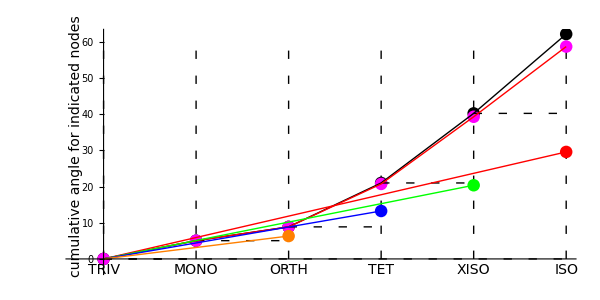

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax,0}}],
Table[Line[{{n,0},{n,yy[nMax,Tmat,pw2]/Degree}}],{n,0,nMax}]},     (* vertical dashed lines *)
Point[{#,yy[#,Tmat,pw2]/Degree}]&/@Range[0,nMax],   (* pw2 *)
If[WantPW3=="WantPW3",
{Magenta,PointSize[.015],Point[{#,yy[#,Tmat,pw3]/Degree}]&/@Range[0,nMax]}], (* pw3 *)
{Dashing[{.01,.02}],         (* horizontal dashed steps, pw2 only*)
Line[{{#,      yy[#,Tmat,pw2]/Degree},
   {#+1,yy[#,Tmat,pw2]/Degree}}]&/@Range[0,nMax-1]},
 Line[{#,yy[#,Tmat,pw2]/Degree}&/@Range[0,nMax]],      (* the main polygonal line, pw2 *)
If[WantPW3=="WantPW3",
{Red,Line[{#,yy[#,Tmat,pw3]/Degree}&/@Range[0,nMax]]}],  (* the main polygonal line, pw3 *)
If[True,{
{Red,        Line[{{0,0},{5,AngleMatrix[Tmat,Closest[Tmat,ISO]  ]/Degree}}],Point[{5,AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree}]},
{Green,   Line[{{0,0},{4,AngleMatrix[Tmat,Closest[Tmat,XISO]]/Degree}}],Point[{4,AngleMatrix[Tmat,Closest[Tmat,XISO]]/Degree}]},
{Blue,     Line[{{0,0},{3,AngleMatrix[Tmat,Closest[Tmat,TET  ]]/Degree}}],Point[{3,AngleMatrix[Tmat,Closest[Tmat,TET  ]]/Degree}]},
{Orange,Line[{{0,0},{2,AngleMatrix[Tmat,Closest[Tmat,ORTH]]/Degree}}],Point[{2,AngleMatrix[Tmat,Closest[Tmat,ORTH]]/Degree}]}}],
Text[Style[Σn[#],14],{#,-3}]&/@Range[0,nMax],
Text[Style["cumulative angle for indicated nodes",14],{-.3,.5yy[nMax,Tmat,pw2]/Degree},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

#### Difference between Pathway 2 and 3

Tmat is TmatBrownTypo

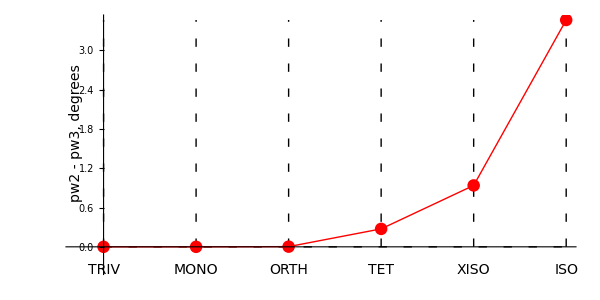

```mathematica
MatrixNote[Tmat]
Graphics[{
{Dashing[{.01,.02}],Line[{{0,0},{5,0}}],Table[Line[{{n,0},{n,dymax/Degree}}],{n,0,5}]},
{Red,PointSize[.015],Point[{#,ydiff[#,Tmat]/Degree}]&/@Range[0,5]}, (* points *)
{Red,Line[{#,ydiff[#,Tmat]/Degree}&/@Range[0,5]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax/Degree}]&/@Range[0,5],
Text[Style["pw2 - pw3, degrees",14],{-.3,.5dymax/Degree},{0,0},{0,1}]},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> False,AxesOrigin->{0,0}]
```

## For comparison

Tmat is TmatBrownTypo

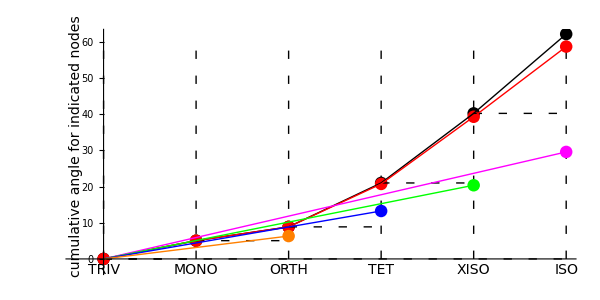

-Graphics-

Tmat is TmatBrownNew

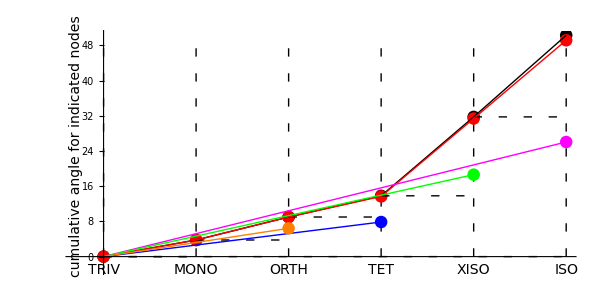

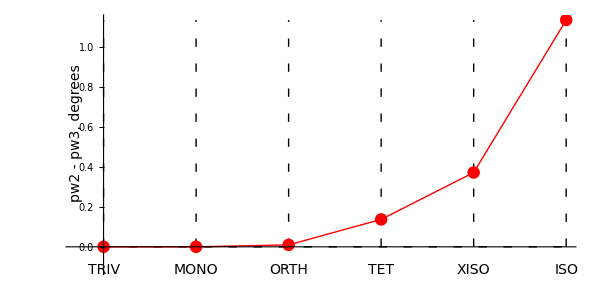

Tmat is TmatSSA2023

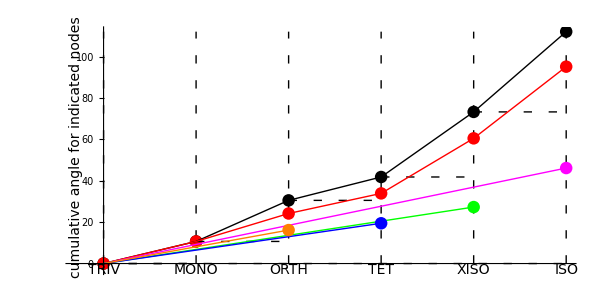

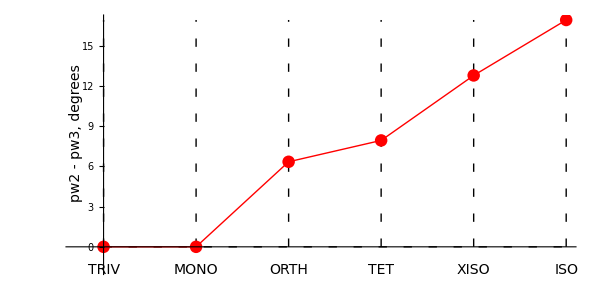

Tmat is TmatDefeat

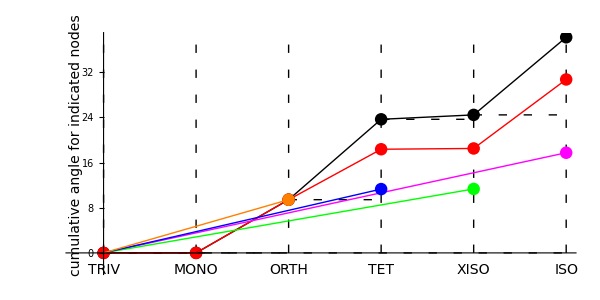

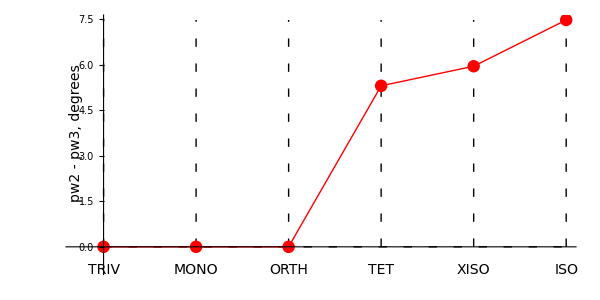

Tmat is TmatMar17

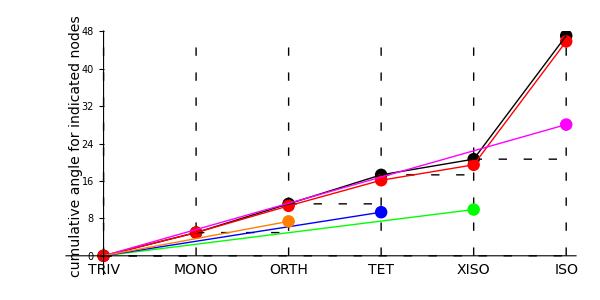

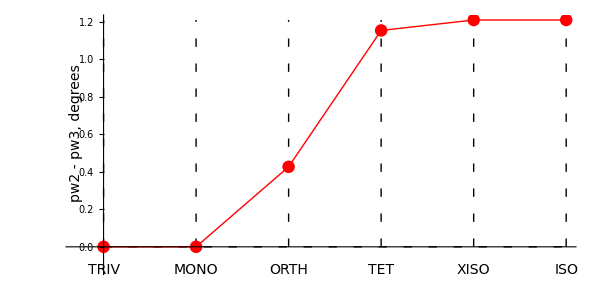

Tmat is TmatIgel